```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Thu 18 Jan 2018 23:45:26

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.0.0 (September 4, 2016)

## At Day 11

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

## 5 Further Topics in Calculus

## Lab 34: Conic Sections and Parametric Equations

Introduction

Demonstration: Plane Cross Sections of the Surface of a Cone

Exercises:

a.

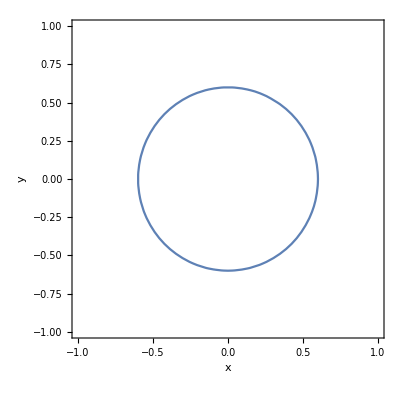

```mathematica
ContourPlot[x^2+y^2==0.6^2,{x,-1,1},{y,-1,1},FrameLabel->Automatic]
```

The equation of a unit circle is x^2+y^2==1.

b.

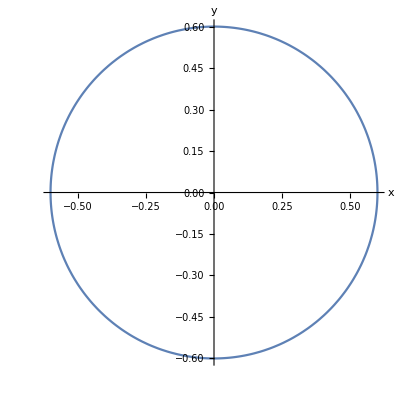

```mathematica
ParametricPlot[0.6{Cos[θ],Sin[θ]},{θ,0,2π},AxesLabel->{x,y}]
```

c.

d.

The standard form of an ellipse is x^2/a^2+y^2/b^2==1.

e.

```mathematica
x^2/a^2+y^2/b^2==1
SCMAF[%,RA,{All,{x==a Cos[θ],y==b Sin[θ]}},Apply->Simplify]
```

x^2/a^2+y^2/b^2==1

True

f.

```mathematica
√((x+f)^2+y^2)+√((x-f)^2+y^2)==c
SCMAF[%,RA,{All,c==2a},
SCMoveTerm,{All,√((x-f)^2+y^2)},
#^2&,All,Level->{1},Apply->Expand,
SCEqMove,{All,4a √((-f+x)^2+y^2)},
#^2&,All,Level->{1},Apply->Expand,
SCMoveTerm,{All,At[2]},
SCEliminate,{All,x^2/a^2+y^2/b^2==1,y^2},
Collect,{All,x}]
```

√((-f+x)^2+y^2)+√((f+x)^2+y^2)==c

-16 a^4+16 a^2 f^2+16 a^2 x^2-16 f^2 x^2+16 b^2 (a^2-x^2)==0

-16 a^4+16 a^2 b^2+16 a^2 f^2+(16 a^2-16 b^2-16 f^2) x^2==0

To satisfy this equation for any x,

```mathematica
SCSolve[16 a^2-16 b^2-16 f^2==0,f]
```

{{f==-√(a^2-b^2)},{f==√(a^2-b^2)}}

```mathematica
SCSolve[-16 a^4+16 a^2 b^2+16 a^2 f^2==0,f]
```

{{f==-√(a^2-b^2)},{f==√(a^2-b^2)}}

g.

The standard form of a hyperbola is x^2/a^2-y^2/b^2==1.

h.

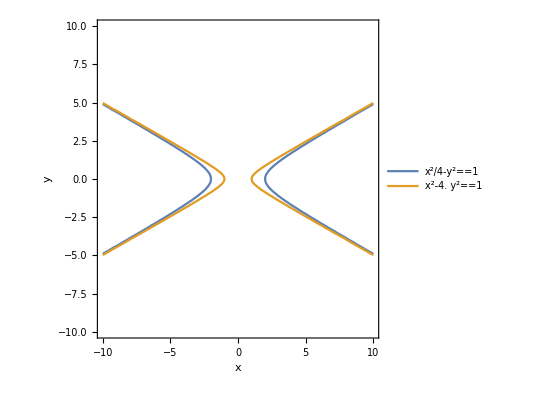

```mathematica
ContourPlot[Evaluate@{(x^2/a^2-y^2/b^2==1/.{a->2,b->1}),(x^2/a^2-y^2/b^2==1/.{a->1,b->0.5})},{x,-10,10},{y,-10,10},PlotLegends->"Expressions",FrameLabel->Automatic]
```

i.

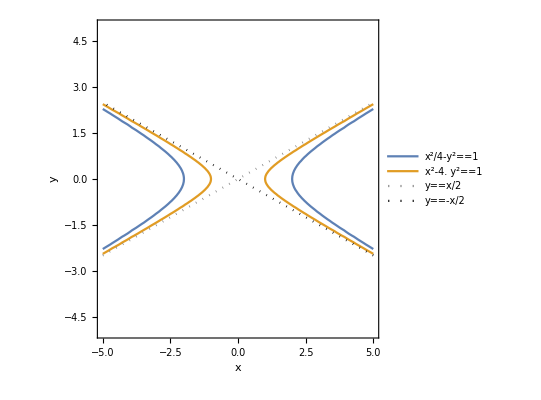

```mathematica
ContourPlot[Evaluate@{(x^2/a^2-y^2/b^2==1/.{a->2,b->1}),(x^2/a^2-y^2/b^2==1/.{a->1,b->0.5}),(y==b/a x/.{a->2,b->1}),(y==-b/a x/.{a->2,b->1})},{x,-5,5},{y,-5,5},ContourStyle->{Automatic,Automatic,{Gray,Dotted},{Black,Dotted}},PlotLegends->"Expressions",Axes->True,FrameLabel->Automatic]
```

j.

```mathematica
√((x+f)^2+y^2)-√((x-f)^2+y^2)==c
SCMAF[%,RA,{All,c==2a},
SCMoveTerm,{All,√((x-f)^2+y^2)},
#^2&,All,Level->{1},Apply->Expand,
SCEqMove,{All,4a √((-f+x)^2+y^2)},
#^2&,All,Level->{1},Apply->Expand,,
SCMoveTerm,{All,At[2]},
SCEliminate,{All,x^2/a^2-y^2/b^2==1,y^2},
Collect,{All,x}]
```

-√((-f+x)^2+y^2)+√((f+x)^2+y^2)==c

16 a^2 f^2-32 a^2 f x+16 a^2 x^2+16 a^2 y^2==16 a^4-32 a^2 f x+16 f^2 x^2

-16 a^4+16 a^2 f^2+16 a^2 x^2-16 f^2 x^2-16 b^2 (a^2-x^2)==0

-16 a^4-16 a^2 b^2+16 a^2 f^2+(16 a^2+16 b^2-16 f^2) x^2==0

To satisfy this equation for any x,

```mathematica
SCSolve[16 a^2+16 b^2-16 f^2==0,f]
```

{{f==-√(a^2+b^2)},{f==√(a^2+b^2)}}

```mathematica
SCSolve[-16 a^4-16 a^2 b^2+16 a^2 f^2==0,f]
```

{{f==-√(a^2+b^2)},{f==√(a^2+b^2)}}

k.

l.

The standard equation for a hyperboloid is x^2/a^2+y^2/b^2-z^2/c^2==1.

```mathematica
ContourPlot3D[Evaluate[x^2/a^2+y^2/b^2-z^2/c^2==1/.{a->1,b->1,c->1}],{x,-5,5},{y,-5,5},{z,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
x^2/a^2+y^2/b^2-z^2/c^2==1
SCMAF[%,RA,{All,{a==1,b==1,c==1}},
RA,{At[1],{x==Cos[u]+ v Sin[u],y== Sin[u]- v Cos[u]}},
SCSolve,{All,z,Rule->True},Apply->FullSimplify]
```

x^2/a^2+y^2/b^2-z^2/c^2==1

-z^2+(-v Cos[u]+Sin[u])^2+(Cos[u]+v Sin[u])^2==1

{{z→-√(v^2)},{z→√(v^2)}}

```mathematica
ParametricPlot3D[{Cos[u]+v Sin[u],Sin[u]-v Cos[u],v},{u,0,2π},{v,-10,10},AxesLabel->{x,y,z}]
```

-Graphics3D-

m.

The standard equation for an ellipsoid is x^2/a^2+y^2/b^2+z^2/c^2==1.

```mathematica
ContourPlot3D[Evaluate[x^2/a^2+y^2/b^2+z^2/c^2==1/.{a->3,b->2,c->1}],{x,-3,3},{y,-3,3},{z,-3,3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
x^2/a^2+y^2/b^2+z^2/c^2==1
SCMAF[%,RA,{At[1],{x==a Cos[u]Sin[v],y==b Sin[u]Sin[v],z==c Cos[v]}},Apply->FullSimplify]
```

x^2/a^2+y^2/b^2+z^2/c^2==1

True

```mathematica
ParametricPlot3D[Evaluate[{a Cos[u]Sin[v],b Sin[u]Sin[v],c Cos[v]}/.{a->3,b->2,c->1}],{u,0,2π},{v,0,2π},PlotRange->{{-3,3},{-3,3},{-3,3}},AxesLabel->{x,y,z}]
```

-Graphics3D-

## Lab 35: Hyperbolic Functions

Introduction

```mathematica
x^2+y^2==1
SCMAF[%,RA,{At[1],{x==Cos[θ],y==Sin[θ]}},Apply->Simplify]
```

x^2+y^2==1

True

```mathematica
x^2-y^2==1
SCMAF[%,RA,{At[1],{x==Cosh[θ],y==Sinh[θ]}},Apply->Simplify]
```

x^2-y^2==1

True

Defining cosh(μ) and sinh(μ).

Exercises:

a, b.

```mathematica
x^2-y^2==1
SCMAF[%,SCSolve,{All,y}]
```

x^2-y^2==1

{{y==-√(-1+x^2)},{y==√(-1+x^2)}}

```mathematica
SCAFE[∫_1^x √(-1+s^2)ⅆs,SCEvalInt]
SCMAF[%,Refine,{All,x≥1},
SCEliminate,{At[2],y==√(-1+x^2),√(-1+x^2)}]
```

ConditionalExpression[∫_1^x √(-1+s^2)ⅆs==1/2 (x √(-1+x^2)-Log[x+√(-1+x^2)]),x≥1]

∫_1^x √(-1+s^2)ⅆs==1/2 (x √(-1+x^2)-Log[x+√(-1+x^2)])

∫_1^x √(-1+s^2)ⅆs==1/2 (x y-Log[x+y])

c.

```mathematica
S==2((x y)/2-∫_1^x √(-1+s^2)ⅆs)
SCMAF[%,RR,{At[2],{∫_1^x_ √(-1+s^2)ⅆs==1/2 (x y-Log[x+y]),x==Cosh[μ],y==Sinh[μ]}},
FullSimplify,{At[2],Assumptions->μ>0}]
```

S==2 ((x y)/2-∫_1^x √(-1+s^2)ⅆs)

S==2 (1/2 Cosh[μ] Sinh[μ]+1/2 (Log[Cosh[μ]+Sinh[μ]]-Cosh[μ] Sinh[μ]))

S==μ

d.

```mathematica
S==2((x y)/2-∫_1^x √(-1+s^2)ⅆs)
SCMAF[%,RA,{All,{S==μ,∫_1^x_ √(-1+s^2)ⅆs==1/2 (x y-Log[x+y])}},
FullSimplify,{At[2],Assumptions->μ>0},
ⅇ^#&,All,Level->{1}]
```

S==2 ((x y)/2-∫_1^x √(-1+s^2)ⅆs)

μ==Log[x+y]

ⅇ^μ==x+y

e.

```mathematica
SCAFE[∫_1^x -√(-1+s^2)ⅆs,SCEvalInt]
SCMAF[%,Refine,{All,x≥1},
SCEliminate,{At[2],y==-√(-1+x^2),√(-1+x^2)},
SCMultEq,{All,-1}]
```

ConditionalExpression[∫_1^x -√(-1+s^2)ⅆs==1/2 (-x √(-1+x^2)+Log[x+√(-1+x^2)]),x≥1]

-∫_1^x √(-1+s^2)ⅆs==1/2 (x y+Log[x-y])

∫_1^x √(-1+s^2)ⅆs==1/2 (-x y-Log[x-y])

```mathematica
-S/2==(x y)/2-∫_1^x -√(-1+s^2)ⅆs
SCMAF[%,SCFactorInt,At[2],
RR,{All,{S==-μ,∫_1^x_ √(-1+s^2)ⅆs==1/2 (-x y-Log[x-y])}},
SCMultEq,{All,-2},Apply->ExpandAll,
ⅇ^#&,All,Level->{1}]
```

-S/2==(x y)/2-∫_1^x -√(-1+s^2)ⅆs

-μ==Log[x-y]

ⅇ^-μ==x-y

```mathematica
{ⅇ^μ==x+y,ⅇ^-μ==x-y}
SCMAF[%,RA,{All,{x==Cosh[μ],y==Sinh[μ]}},
SCSolve,{All,{Cosh[μ],Sinh[μ]}},Apply->Expand,
SCFactor,{{ⅇ^-μ/2+ⅇ^μ/2,1/2},{-ⅇ^-μ/2+ⅇ^μ/2,1/2}}]
```

{ⅇ^μ==x+y,ⅇ^-μ==x-y}

{Cosh[μ]==ⅇ^-μ/2+ⅇ^μ/2,Sinh[μ]==-ⅇ^-μ/2+ⅇ^μ/2}

{Cosh[μ]==1/2 (ⅇ^-μ+ⅇ^μ),Sinh[μ]==1/2 (-ⅇ^-μ+ⅇ^μ)}

Properties of cosh(μ) and sinh(μ).

f.

```mathematica
{cosh[μ]==(ⅇ^μ+ⅇ^-μ)/2,sinh[μ]==(ⅇ^μ-ⅇ^-μ)/2}
SCMAF[%,RA,{All,μ==1},Apply->N]
```

{cosh[μ]==1/2 (ⅇ^-μ+ⅇ^μ),sinh[μ]==1/2 (-ⅇ^-μ+ⅇ^μ)}

{cosh[1.]==1.54308,sinh[1.]==1.1752}

```mathematica
{cosh[μ]==Cosh[μ],sinh[μ]==Sinh[μ]}/.μ->1//N
```

{cosh[1.]==1.54308,sinh[1.]==1.1752}

g.

```mathematica
{tanh[x]==sinh[x]/cosh[x],tanh[x]==sinh[x]/cosh[x]}
SCMAF[%,RA,{All,{cosh[μ_]==(ⅇ^μ+ⅇ^-μ)/2,sinh[μ_]==(ⅇ^μ-ⅇ^-μ)/2}}]
```

{tanh[x]==sinh[x]/cosh[x],tanh[x]==sinh[x]/cosh[x]}

{tanh[x]==(-ⅇ^-x+ⅇ^x)/(ⅇ^-x+ⅇ^x),tanh[x]==(-ⅇ^-x+ⅇ^x)/(ⅇ^-x+ⅇ^x)}

h.

```mathematica
SCAFE[ⅆCosh[x]/ⅆx,TrigToExp,Cosh[x],ApplyAll->SCEvalDeriv]
SCMAF[%,SCExpToTrig,At[2]]
```

ⅆCosh[x]/ⅆx==-ⅇ^-x/2+ⅇ^x/2

ⅆCosh[x]/ⅆx==Sinh[x]

```mathematica
SCAFE[ⅆSinh[x]/ⅆx,TrigToExp,Sinh[x],ApplyAll->SCEvalDeriv]
SCMAF[%,SCExpToTrig,At[2]]
```

ⅆSinh[x]/ⅆx==ⅇ^-x/2+ⅇ^x/2

ⅆSinh[x]/ⅆx==Cosh[x]

```mathematica
SCAFE[{ⅆCosh[x]/ⅆx,ⅆSinh[x]/ⅆx},SCEvalDeriv]//Thread
```

{ⅆCosh[x]/ⅆx==Sinh[x],ⅆSinh[x]/ⅆx==Cosh[x]}

i.

```mathematica
SCARA[Underscript[Limit, x->∞][Sech[x]],Sech[x]==2/(ⅇ^x+ⅇ^-x),Apply->SCEvalLimit]
```

Limit_(x→∞)[Sech[x]]==0

```mathematica
SCARA[Underscript[Limit, x->∞][Csch[x]],Csch[x]==2/(ⅇ^x-ⅇ^-x),Apply->SCEvalLimit]
```

Limit_(x→∞)[Csch[x]]==0

```mathematica
SCAFE[{Underscript[Limit, x->∞][Sech[x]],Underscript[Limit, x->∞][Csch[x]]},SCEvalLimit]//Thread
```

{Limit_(x→∞)[Sech[x]]==0,Limit_(x→∞)[Csch[x]]==0}

## Lab 36: Sequences

Introduction

Exercises:

a.

```mathematica
Subscript[f, n]==5 4^n;
```

b.

c.

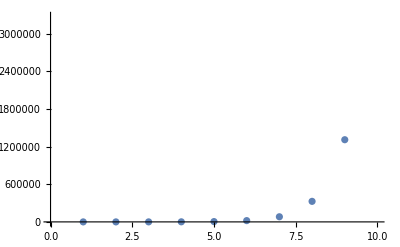

```mathematica
ListPlot@Table[5 4^n,{n,10}]
```

d.

e.

```mathematica
SCAFE[Underscript[Limit, n->∞][a b^n],SCEvalLimit]
```

ConditionalExpression[Limit_(n→∞)[a b^n]==∞,a>0&&Log[b]>0]

f.

```mathematica
Subscript[f, n+1]>Subscript[f, n]
SCMAF[%,RA,{All,Subscript[f, n_]->5 4^n},
Reduce,{All,n,Reals}]
```

f_(1+n)>f_n

5 4^(1+n)>5 4^n

True

g.

```mathematica
SCAFE[Underscript[Limit, n->∞][(-1)^n/n],SCEvalLimit]
```

Limit_(n→∞)[(-1)^n/n]==0

h.

```mathematica
Subscript[f, n+1]>Subscript[f, n]
SCMAF[%,RA,{All,Subscript[f, n_]->(-1)^n/n},
Reduce,{All,n,Reals}]
```

f_(1+n)>f_n

(-1)^(1+n)/(1+n)>(-1)^n/n

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

SCMAF::stopped: Stopped due to error.

Reduce[(-1)^(1+n)/(1+n)>(-1)^n/n,n,ℝ]

```mathematica
Subscript[f, n+1]>Subscript[f, n]
SCMAF[%,RA,{All,Subscript[f, n_]->(-1)^n/n},
Simplify,{All,Assumptions->{n>0,n∈Integers}}]
```

f_(1+n)>f_n

(-1)^(1+n)/(1+n)>(-1)^n/n

(-1)^(1+n)>0

i.

```mathematica
Subscript[s, k]==∑_(n=1)^k Subscript[f, n]
SCMAF[%,RA,{At[2],Subscript[f, n_]->n},Apply->SCEvalSum]
```

s_k==∑_(n=1)^k f_n

s_k==1/2 k (1+k)

j.

```mathematica
Subscript[s, k]==∑_(n=1)^k Subscript[f, n]
SCMAF[%,RA,{At[2],Subscript[f, n_]->(1/2)^n},Apply->SCEvalSum]
```

s_k==∑_(n=1)^k f_n

s_k==2^-k (-1+2^k)

k, l.

s_k==2^-k (-1+2^k)

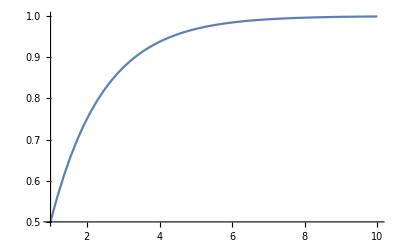

```mathematica
Subscript[s, k]==2^-k (-1+2^k)
SCMAF[%,Plot,{At[2],{k,1,10}},Part->2]
```

m.

```mathematica
SCARA[Underscript[Limit, k->∞][Subscript[s, k]],Subscript[s, k]==2^-k (-1+2^k),Apply->SCEvalLimit]
```

Limit_(k→∞)[s_k]==1

## Lab 37: An Introduction to Series

Geometric series

a.

```mathematica
Subscript[S, k]==∑_(n=1)^k 12/5^(n-1)
SCMAF[%,SCEvalSum,At[2]]
```

S_k==∑_(n=1)^k 12 5^(1-n)

S_k==3 5^(1-k) (-1+5^k)

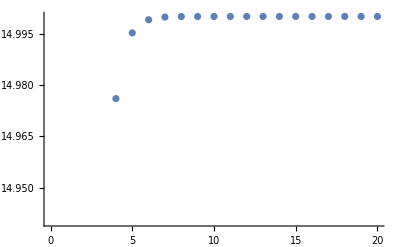

```mathematica
ListPlot@Table[3 5^(1-k) (-1+5^k),{k,20}]
```

b.

```mathematica
SCAFE[Underscript[Limit, k->∞][∑_(n=1)^k 12/5^(n-1)],SCEvalSum,Apply->SCEvalLimit]
```

Limit_(k→∞)[∑_(n=1)^k 12 5^(1-n)]==15

```mathematica
SCAFE[∑_(n=1)^∞ 12/5^(n-1),SCEvalSum,Apply->ExpandAll]
```

∑_(n=1)^∞ 12 5^(1-n)==15

d.

```mathematica
SCAFE[∑_(n=1)^∞ 12/5^n,SCFactor,{5^-n,1/5,Times->True}]
```

∑_(n=1)^∞ 12 5^-n==12/5 ∑_(n=1)^∞ 1·5^(1-n)

e.

```mathematica
Subscript[S, k]==∑_(n=1)^k 12/5^n
SCMAF[%,SCEvalSum,At[2],Apply->ExpandAll]
```

S_k==∑_(n=1)^k 12 5^-n

S_k==3-3 5^-k

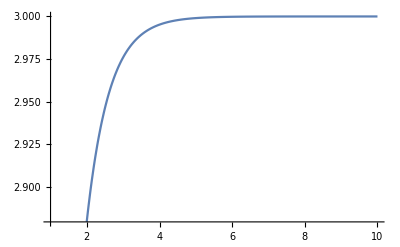

```mathematica
Plot[3-3 5^-k,{k,1,10}]
```

```mathematica
Subscript[S, ∞]==∑_(n=1)^∞ 12/5^n
SCMAF[%,SCEvalSum,At[2]]
```

S_∞==∑_(n=1)^∞ 12 5^-n

S_∞==3

f.

```mathematica
Subscript[S, k]==∑_(n=1)^k (12/5)^n
SCMAF[%,SCEvalSum,At[2],Apply->ExpandAll,
FullSimplify,At[2]]
```

S_k==∑_(n=1)^k (12/5)^n

S_k==-12/7+1/7 5^-k 12^(1+k)

S_k==12/7 (-1+(12/5)^k)

Keep in mind the convergence of geometric series.

```mathematica
Subscript[S, ∞]==∑_(n=1)^∞ a r^(n-1)
SCMAF[%,SCEvalSum,At[2]]
```

S_∞==∑_(n=1)^∞ a r^(-1+n)

S_∞==-a/(-1+r)

```mathematica
Subscript[S, ∞]==∑_(n=1)^∞ a r^(n-1)
SCMAF[%,SCEvalSum,{At[2],Assumptions->{Abs[r]≥1}}]
```

S_∞==∑_(n=1)^∞ a r^(-1+n)

Sum::div: Sum does not converge.

SCMAF::stopped: Stopped due to error.

S_∞==∑_(n=1)^∞ a r^(-1+n)

P-series

```mathematica
Subscript[S, k]==∑_(n=1)^k 1/n
SCMAF[%,SCEvalSum,At[2]]
```

S_k==∑_(n=1)^k 1/n

S_k==HarmonicNumber[k]

S_k==HarmonicNumber[k]

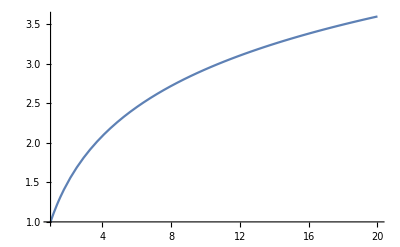

```mathematica
Subscript[S, k]==HarmonicNumber[k]
SCMAF[%,Plot,{At[2],{k,1,20}},Part->2]
```

```mathematica
Subscript[S, k]==∑_(n=1)^k 1/n^p
SCMAF[%,SCEvalSum,At[2]]
```

S_k==∑_(n=1)^k n^-p

S_k==HarmonicNumber[k,p]

{S_k,S_k,S_k,S_k}=={HarmonicNumber[k,1/3],HarmonicNumber[k,1/2],HarmonicNumber[k,4/3],HarmonicNumber[k,3/2]}

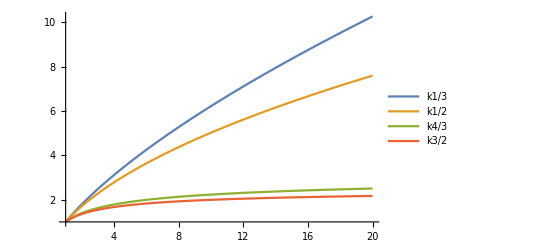

```mathematica
Table[Subscript[S, k]==HarmonicNumber[k,p],{p,{1/3,1/2,1+1/3,1+1/2}}]//Thread[#,Equal]&
SCMAF[%,Plot,{At[2],{k,1,20},PlotLegends->"Expressions"},Part->2]
```

## Lab 38: Convergence Tests for Series

Integral test
Given N∈ℤ, where f(n) is non-negative and monotonically decreasing on [N,∞),
∑_(n=N)^∞ f(n) converges if and only if ∫_N^∞ f(x)ⅆx converges.

a, b, c.

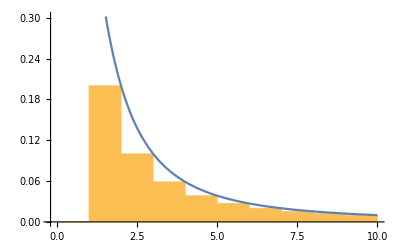

```mathematica
Show[RectangleChart[Prepend[Table[{1,1/(n^2+1)},{n,2,10}],{1,0}],BarSpacing->None],Plot[1/(x^2+1),{x,1,10}]]
```

d.

```mathematica
SCAFE[∑_(n=1)^k 1/(n^2+1),SCEvalSum,All,Apply->FullSimplify]
```

∑_(n=1)^k 1/(1+n^2)==1/2 (-1+π Coth[π]-ⅈ HarmonicNumber[-ⅈ+k]+ⅈ HarmonicNumber[ⅈ+k])

```mathematica
SCAFE[∫_1^k 1/(x^2+1)ⅆx,SCEvalInt,{All,Assumptions->k>1}]
```

∫_1^k 1/(1+x^2)ⅆx==-π/4+ArcTan[k]

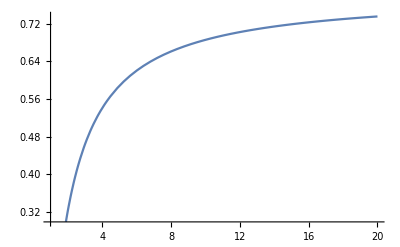

```mathematica
Plot[-π/4+ArcTan[k],{k,1,20}]
```

```mathematica
SCAFE[∫_1^∞ 1/(x^2+1)ⅆx,SCEvalInt]
```

∫_1^∞ 1/(1+x^2)ⅆx==π/4

e.

f.

Comparison test
If ∑_(n=N)^∞ a_n and ∑_(n=N)^∞ b_n are series with 0≤a_n≤b_n for all n≥N, then
1. if ∑_(n=N)^∞ a_n diverges, then ∑_(n=N)^∞ b_n diverges and
2. if ∑_(n=N)^∞ b_n converges, then ∑_(n=N)^∞ a_n converges.

a, b.

```mathematica
1/(n^2+1)≤1/n^p
SCMAF[%,RA,{All,p==2},
Reduce,{All,n}]
```

1/(1+n^2)≤n^-p

1/(1+n^2)≤1/n^2

n<0||n>0

```mathematica
SCAFE[∑_(n=1)^∞ 1/(n^2+1),SCEvalSum]
```

∑_(n=1)^∞ 1/(1+n^2)==1/2 (-1+π Coth[π])

c, d.

```mathematica
(6^(n-1)-1)/11^(n-1)≤a r^(n-1)
SCMAF[%,RA,{All,{a==1,r==6/11}},
Reduce,{All,n,Reals}]
```

11^(1-n) (-1+6^(-1+n))≤a r^(-1+n)

11^(1-n) (-1+6^(-1+n))≤(6/11)^(-1+n)

True

```mathematica
SCAFE[∑_(n=1)^∞ (6^(n-1)-1)/11^(n-1),SCEvalSum]
```

∑_(n=1)^∞ 11^(1-n) (-1+6^(-1+n))==11/10

e.

f, g.

```mathematica
ⅇ^n/n≥1/n^p
SCMAF[%,RA,{At[2],p==1},
Reduce,{All,n,Reals}]
```

ⅇ^n/n≥n^-p

ⅇ^n/n≥1/n

n≠0

Ratio test
Given the series ∑_(n=N)^∞ a_n and lim_(n→∞) |(a_(n+1))/a_n|=L, then
1. if L<1 then the series converges,
2. if L>1 then the series diverges,
3. if L=1 then the test is inconclusive.

a, b.

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[a, n+1]/Subscript[a, n]],Subscript[a, n_]->1/(n^2+1),Apply->SCEvalLimit]
```

Limit_(n→∞)[(a_(1+n))/a_n]==1

c, d.

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[a, n+1]/Subscript[a, n]],Subscript[a, n_]->e^n/(n!),Apply->SCEvalLimit]
```

Limit_(n→∞)[(a_(1+n))/a_n]==0

## Lab 39: Alternating Series

Demonstration: Sum of the Alternating Harmonic Series (I)

a, b, c, d.

```mathematica
SCAFE[Table[∑_(n=k)^(k+1) (-1)^(n-1)/n,{k,1,3,2}],SCEvalSum]
```

{∑_(n=1)^2 (-1)^(-1+n)/n,∑_(n=3)^4 (-1)^(-1+n)/n}=={1/2,1/12}

e.

```mathematica
SCAFE[∫_1^2 1/x ⅆx,SCEvalInt]
```

∫_1^2 1/x ⅆx==Log[2]

```mathematica
SCAFE[Underscript[Limit, k->∞][∑_(n=1)^k (-1)^(n-1)/n],SCEvalSum,Apply->SCEvalLimit]
```

Limit_(k→∞)[∑_(n=1)^k (-1)^(-1+n)/n]==Log[2]

Alternating series test
∑_(n=1)^∞ ((-1)^(n-1)a_n) converges if |a_(n+1)|<|a_n| for all n≥1 and lim_(n→∞) a_n=0.

f.

g.

h.

i.

```mathematica
Abs[(-3/5)^(n+1)]<Abs[(-3/5)^n]
SCMAF[%,Reduce,{All,n,Integers}]
```

|(-3/5)^(1+n)|<|(-3/5)^n|

n∈ℤ

j.

```mathematica
SCAFE[Underscript[Limit, n->∞][(3/5)^n],SCEvalLimit]
```

Limit_(n→∞)[(3/5)^n]==0

k.

l.

m.

## Lab 40: Taylor Series

a, b, c.

```mathematica
SCARA[∑_(n=0)^9 Subscript[Derivative[n][f][x], x==0]/(n!)x^n,f->Function[{x},Cos[x]],Apply->SCEvalSum]
SCMAF[%,SCEvalEqSub,At[2]]
```

∑_(n=0)^9 (x^n (f^(n)[x])_(x==0))/(n!)==1/2 x^2 (-Cos[x])_(x==0)+1/720 x^6 (-Cos[x])_(x==0)+Cos[x]_(x==0)+1/24 x^4 Cos[x]_(x==0)+(x^8 Cos[x]_(x==0))/40320+x (-Sin[x])_(x==0)+1/120 x^5 (-Sin[x])_(x==0)+(x^9 (-Sin[x])_(x==0))/362880+1/6 x^3 Sin[x]_(x==0)+(x^7 Sin[x]_(x==0))/5040

∑_(n=0)^9 (x^n (f^(n)[x])_(x==0))/(n!)==1-x^2/2+x^4/24-x^6/720+x^8/40320

```mathematica
∑_(n=0)^∞ Subscript[Derivative[n][f][x], x==0]/(n!)x^n==Series[Cos[x],{x,0,9}]
```

∑_(n=0)^∞ (x^n (f^(n)[x])_(x==0))/(n!)==1-x^2/2+x^4/24-x^6/720+x^8/40320+O[x]^10

```mathematica
SCAFE[Cos[x],SCPowerSeries,{All,n}]
```

Cos[x]==∑_(n=0)^∞ ((-1)^n x^(2 n))/((2 n)!)

d, e.

```mathematica
SCARA[∑_(n=0)^9 Subscript[Derivative[n][f][x], x==0]/(n!)x^n,f->Function[{x},ArcSin[x]],Apply->SCEvalSum]
SCMAF[%,SCEvalEqSub,At[2]]
```

∑_(n=0)^9 (x^n (f^(n)[x])_(x==0))/(n!)==1/2 x^2 (x/((1-x^2)^(3/2)))_(x==0)+x (1/(√(1-x^2)))_(x==0)+1/24 x^4 ((15 x^3)/((1-x^2)^(7/2))+(9 x)/((1-x^2)^(5/2)))_(x==0)+1/6 x^3 ((3 x^2)/((1-x^2)^(5/2))+1/((1-x^2)^(3/2)))_(x==0)+1/120 x^5 ((75 x^2)/((1-x^2)^(7/2))+9/((1-x^2)^(5/2))+3 x^2 ((35 x^2)/((1-x^2)^(9/2))+5/((1-x^2)^(7/2))))_(x==0)+1/720 x^6 ((420 x^3)/((1-x^2)^(9/2))+(180 x)/((1-x^2)^(7/2))+9 x ((35 x^2)/((1-x^2)^(9/2))+5/((1-x^2)^(7/2)))+3 x^2 ((70 x)/((1-x^2)^(9/2))+5 x ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))))_(x==0)+1/5040 x^7 ((2100 x^2)/((1-x^2)^(9/2))+180/((1-x^2)^(7/2))+60 x^2 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+9 ((35 x^2)/((1-x^2)^(9/2))+5/((1-x^2)^(7/2)))+15 x ((70 x)/((1-x^2)^(9/2))+5 x ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2))))+3 x^2 ((630 x^2)/((1-x^2)^(11/2))+70/((1-x^2)^(9/2))+5 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+5 x ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))))_(x==0)+1/40320 x^8 ((15120 x^3)/((1-x^2)^(11/2))+(5040 x)/((1-x^2)^(9/2))+180 x ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+60 x^2 ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))+24 ((70 x)/((1-x^2)^(9/2))+5 x ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2))))+21 x ((630 x^2)/((1-x^2)^(11/2))+70/((1-x^2)^(9/2))+5 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+5 x ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))))+3 x^2 ((1260 x)/((1-x^2)^(11/2))+70 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+10 ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))+5 x ((1386 x^2)/((1-x^2)^(13/2))+126/((1-x^2)^(11/2))+7 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+7 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))))))_(x==0)+1/362880 x^9 ((75600 x^2)/((1-x^2)^(11/2))+5040/((1-x^2)^(9/2))+1680 x^2 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+180 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+300 x ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))+60 x^2 ((1386 x^2)/((1-x^2)^(13/2))+126/((1-x^2)^(11/2))+7 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+7 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))))+45 ((630 x^2)/((1-x^2)^(11/2))+70/((1-x^2)^(9/2))+5 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+5 x ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))))+27 x ((1260 x)/((1-x^2)^(11/2))+70 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+10 ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))+5 x ((1386 x^2)/((1-x^2)^(13/2))+126/((1-x^2)^(11/2))+7 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+7 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2))))))+3 x^2 ((13860 x^2)/((1-x^2)^(13/2))+1260/((1-x^2)^(11/2))+70 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+70 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2))))+15 ((1386 x^2)/((1-x^2)^(13/2))+126/((1-x^2)^(11/2))+7 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+7 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))))+5 x ((2772 x)/((1-x^2)^(13/2))+126 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))+14 ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2))))+7 x ((2574 x^2)/((1-x^2)^(15/2))+198/((1-x^2)^(13/2))+9 ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))+9 x ((286 x)/((1-x^2)^(15/2))+11 x ((195 x^2)/((1-x^2)^(17/2))+13/((1-x^2)^(15/2))))))))_(x==0)+ArcSin[x]_(x==0)

∑_(n=0)^9 (x^n (f^(n)[x])_(x==0))/(n!)==x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152

```mathematica
∑_(n=0)^∞ Subscript[Derivative[n][f][x], x==0]/(n!)x^n==Series[ArcSin[x],{x,0,9}]
```

∑_(n=0)^∞ (x^n (f^(n)[x])_(x==0))/(n!)==x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152+O[x]^10

```mathematica
SCAFE[ArcSin[x],SCPowerSeries,{All,n}]
```

ArcSin[x]==∑_(n=0)^∞ (4^-n x^(1+2 n) (2 n)!)/((1+2 n) (n!)^2)

f.

```mathematica
g[x]==x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152
SCMAF[%,SCMultEq,{All,6},
RA,{All,x==1/2},Apply->N]
```

g[x]==x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152

6 g[x]==6 x+x^3+(9 x^5)/20+(15 x^7)/56+(35 x^9)/192

6. g[0.5]==3.14151

```mathematica
SCARA[6arcSin[1/2],{arcSin[x_]->∑_(n=0)^∞ (4^-n x^(1+2 n) (2 n)!)/((1+2 n) (n!)^2)},Apply->SCEvalSum]
```

6 arcSin[1/2]==π